## Initialization

Things like /. kxy2κList sometimes don’t do what I want - for example, using κ+Pi instead of κ in plot arguments doesn’t shift the lines, because kxy2κList remains the same. Define a function if this is the case.

```mathematica
On[Assert]
```

## Constants

### Lattice vectors

I follow Tom’s convention on vectors. I also set the lattice constant a = 1. The “I” and “II” means basis I & II (see my notes).

```mathematica
exp23=Exp[-2*Pi*I/3];
a1vec={0,1};
a2vec={-Sqrt[3]/2,1/2};
a3vec={Sqrt[3]/2,1/2};
ToLatVecList={a1->a1vec,a2->a2vec,a3->a3vec};
(*Transforming from basis II to I, if one cares*)
UII2I={{1,0,0},{0,Exp[I*k.a2],0},{0,0,Exp[I*k.a3]}};
```

### Symmetry operators

These are written in the sublattice basis.

```mathematica
C3II={{0,1,0},{0,0,1},{1,0,0}};
MyII={{0,1,0},{1,0,0},{0,0,1}};
ΠII={{-1,0,0},{0,-1,0},{0,0,-1}};
```

#### High symmetry basis states

```mathematica
(*Eigensystem[C3II]*)
ψ0=(1/Sqrt[3])*{1,1,1};
ψR=(1/Sqrt[3])*{exp23,1,1/exp23};
ψL=(1/Sqrt[3])*{1/exp23,1,exp23};
```

MyII has a double root of 1, so we are free to form any linear superposition of them and still get an eigenstate. I chose the state such that they are also eigenstates for the lattice hamiltonian at Γ/K/K’, respectively.

```mathematica
Eigensystem[MyII]
(*ψ0 is the same as C3II*)
ψy1Γ=(1/Sqrt[2])*{-1,1,0};
ψy2Γ=(1/Sqrt[6])*{1,1,-2};
ψy0K=(1/Sqrt[2])*{1,0,1};
ψy1K=(1/Sqrt[2])*{-1,1,0};
ψy2K=(1/Sqrt[3])*{1,1,-1};
```

{{-1,1,1},{{-1,1,0},{0,0,1},{1,1,0}}}

## Kagome lattice - Expansion around Γ

## Constants

I will start with the chiral basis (the eigenstates of the C3 operator), and form linear superpositions of the chiral states.

```mathematica
kNearΓ=d*{kx,ky};(*d is a dummy variable for series expansion*)
kNearK={d*kx,d*ky+Pi*2/3};
kNearKb={d*kx,d*ky-Pi*2/3};(*I'll write K' as Kb*)
kNearΓVecList=Append[ToLatVecList,k->kNearΓ];
kNearKVecList=Append[ToLatVecList,k->kNearK];
kNearKbVecList=Append[ToLatVecList,k->kNearKb];
kxy2QκList={kx->Q*Cos[κ],ky->Q*Sin[κ]};
kxy2κList={kx->Cos[κ],ky->Sin[κ]};
kxy2ZeroList={kx->0,ky->0};
```

#### New basis states

ψp and ψm turn out to not be the nice basis that gives the reduced hamiltonian in Zephy’s thesis. As we will see later, we want to use τ = π/3 for the pseudospin basis. This turns out to be ψy1Γ and ψy2Γ - makes sense.

```mathematica
ψp=Simplify[(ψR+ψL)/Sqrt[2]];
ψm=Simplify[(ψR-ψL)/(I*Sqrt[2])];
ψt1=Simplify[(ψR+Exp[I*τ]*ψL)/Sqrt[2]];(*t for tau*)
ψt2=Simplify[(ψR-Exp[I*τ]*ψL)/Sqrt[2]/I];
ψbs1=Simplify[ψt1/.τ->Pi/3](*bs for Bloch sphere*)
ψbs2=Simplify[ψt2/.τ->Pi/3]
Simplify[ψbs2[[3]]/ψbs2[[2]]]
```

{-(1+(-1)^(1/3))/(√6),(1+(-1)^(1/3))/(√6),0}

{(-ⅈ+(-1)^(5/6))/(√6),(-ⅈ+(-1)^(5/6))/(√6),(-1)^(1/6) √(2/3)}

-2

#### Unitary matrices for basis transformation

```mathematica
ULR={ψ0,ψR,ψL};
Upm={ψ0,ψp,ψm};
Utau={ψ0,ψt1,ψt2};
Ubs={ψ0,ψbs1,ψbs2};
```

## Kagome Hamiltonian

Convention for variable names (followed loosely):

HkagII is in the sublattice basis (using basis II)

HkagIItau is in the pseudospin basis defined by τ

HkagIIbs is in the “nicest” pseudospin basis. For the case of kagome lattice this is τ=π/3

```mathematica
HkagII=-2*{{0,Cos[k.a1],Cos[k.a2]},{Cos[k.a1],0,Cos[k.a3]},{Cos[k.a2],Cos[k.a3],0}};
HkagIIatΓ=Simplify[HkagII/.k.a_->0];
HkagIIatK=Simplify[HkagII/.kNearKVecList/.kxy2ZeroList];
(*HkagIIatKb is the same as at K*)
HkagIItau=Utau.HkagII.Inverse[Utau];
HkagIItaupwr2=Normal[Series[ComplexExpand[HkagIItau/.kNearΓVecList],{d,0,2}]]/.d->1;
(*Expand[Simplify[TrigToExp[UII2I.HkagII.Inverse[UII2I]]]]//MatrixForm*)
```

```mathematica
MatrixForm[HkagIIatΓ]
```

(0 | -2 | -2
-2 | 0 | -2
-2 | -2 | 0)

### Sanity checks

At Γ: this should be diagonal and have a double root for the QBTP.

```mathematica
HkagIItaupwr2atΓ=Simplify[HkagIItaupwr2/.{kx->0,ky->0}];
MatrixForm[HkagIItaupwr2atΓ]
E0Pert=HkagIItaupwr2atΓ[[2,2]];
(*E0Pert will be used in the 1st order perturbation below*)
```

(-4 | 0 | 0
0 | 2 | 0
0 | 0 | 2)

The Hamiltonian at Γ should commute both C3 and My, but at K it only commutes with My:

```mathematica
HkagIIatΓ.C3II-C3II.HkagIIatΓ
HkagIIatΓ.MyII-MyII.HkagIIatΓ
HkagIIatK.C3II-C3II.HkagIIatK(*Non-zero*)
HkagIIatK.MyII-MyII.HkagIIatK
```

{{0,0,0},{0,0,0},{0,0,0}}

{{0,0,0},{0,0,0},{0,0,0}}

{{-2,0,2},{0,2,0},{0,-2,0}}

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
(*{evalsHkagIIFull,evecsHkagIIFullraw}=Eigensystem[Simplify[HkagII/.kNearΓVecList/.{a->1,d->1}]]/.(√(3+2 Cos[√3 kx-ky]+2 Cos[2 ky]+2 Cos[√3 kx+ky]))->Λ[kx,ky]*)
```

Full band structure looks right:

```mathematica
KagomeBands=Eigenvalues[Simplify[HkagII/.VecExprList/.{a->1,d->1}]];
kRange=Pi;
kSteps=100;
kxVals=Subdivide[-kRange,kRange,kSteps];
kyVals=Subdivide[-kRange,kRange,kSteps];
energyGrids=Table[Table[Evaluate[b/. {kx->kxn,ky->kyn}],{kxn,kxVals},{kyn,kyVals}],{b,KagomeBands}];
plots=Table[ListPlot3D[energyGrids[[i]],DataRange->{{-kRange,kRange},{-kRange,kRange}},Mesh->None,PlotLabel->"Band "<>ToString[i],AxesLabel->{"kx","ky","E"},ColorFunction->"Rainbow",Boxed->False,Lighting->"Neutral"],{i,Length[energyGrids]}];
Show[plots,PlotRange->All]
```

### Playing with τ

τ -> Pi/3 gives the right basis for the pseudospin. Other τ doesn’t look so nice.

```mathematica
MatrixForm[Simplify[HkagIItaupwr2/.τ->Pi/3]](*Insert your favorite τ here*)
HkagIINicest=Simplify[HkagIItaupwr2/.τ->Pi/3];
```

(-4+kx^2+ky^2 | ((-ⅈ+√3) kx ky)/(2 √2) | ((-ⅈ+√3) (kx^2-ky^2))/(4 √2)
((ⅈ+√3) kx ky)/(2 √2) | 2-ky^2 | kx ky
((ⅈ+√3) (kx^2-ky^2))/(4 √2) | kx ky | 2-kx^2)

If we solve for the eigenvectors of the full "Nicest" Hamiltonian directly, we see that the ground state only changes at O(k^2) around Γ . Also, the admixtures of ψ0 into the excited band states are also of order O(k^2). Compare this to the 0th order perturbation results below. (Probably should take the root warnings seriously)

```mathematica
(*The codes below shows the claim above, but takes some time to run*){evalsHkagIINicestFull,evecsHkagIINicestFullraw}=Simplify[Eigensystem[HkagIINicest],Assumptions->{kx,ky}∈Reals];
evecsHkagIINicestFull2ndraw=Simplify[Normal[Series[evecsHkagIINicestFullraw/.{kx->d*kx,ky->d*ky},d->0]]/.d->1]
(*Normalized vectors. I was doing some calculations with them that didn't really work out, probably because of the root issue.
I had to use simplify to get rid of most of the Abs functions, so that when I take derivatives w.r.t. kx and ky below I don't get Abs' that can't be evaluated.*)
evecsHkagIINicestFull2nd=Simplify[Normalize[#]&/@evecsHkagIINicestFull2ndraw,Assumptions->{kx,ky}∈Reals];
```

Root::sbr: Because of branch cuts, the series may represent a different root of 8192-6144 d^2 kx^2+1152 d^4 kx^4-6144 d^2 ky^2+2304 d^4 kx^2 ky^2-576 d^6 kx^4 ky^2+1152 d^4 ky^4+384 d^6 kx^2 ky^4-64 d^6 ky^6+(-768+384 d^2 kx^2-72 d^4 kx^4+384 d^2 ky^2-144 d^4 kx^2 ky^2-72 d^4 ky^4) #1+#1^3& for some values of {kx,ky,d}.

General::stop: Further output of Root::sbr will be suppressed during this calculation.

{{-(24 √2)/((ⅈ+√3) (kx^2-ky^2)),(2 kx ky)/(kx^2-ky^2),1},{(kx^2-3 ky^2)/(6 √2 (ⅈ+√3)),-ky/kx,1},{-(-3 kx^2+ky^2)/(6 √2 (ⅈ+√3)),kx/ky,1}}

### The case of τ = π/3 - mapping to pseudospins

We want to get a description of the two excited bands only, since the ground band is pretty decoupled from them. And by “pretty decoupled,” I mean that the off-diagonal terms in the Hamiltonian between the ground band and the excited bands are small in some sense. This “some sense” is made explicit by going to higher order perturbation.

#### 0th order perturbation

This is obtained by trimming off the rows and columns involving the lowest band.

```mathematica
HkagIIPspin0th=HkagIINicest[[2;;3,2;;3]];
(*MatrixForm[HkagIINicest]*)
MatrixForm[HkagIIPspin0th]
```

(2-ky^2 | kx ky
kx ky | 2-kx^2)

Pseudospin 1 and 2 from now on refer to the flatband states and the dispersive band states, respectively.

```mathematica
{evals0th,evecs0thRaw}=Eigensystem[HkagIIPspin0th]
evecs0th=Simplify[Normalize[#]&/@evecs0thRaw,Assumptions->{kx>0,ky>0}]
evecs0thFull=evecs0th.{ψbs1,ψbs2};
(*Technically I should use {kx,ky}∈Reals instead of {kx>0,ky>0}, but this only leaves an unneccary global phase in front of each eigenvector*)
```

{{2,2-kx^2-ky^2},{{kx/ky,1},{-ky/kx,1}}}

{{kx/(√(kx^2+ky^2)),ky/(√(kx^2+ky^2))},{-ky/(√(kx^2+ky^2)),kx/(√(kx^2+ky^2))}}

(Not the best way to plot this, but) we see that the state winds two times around the QBTP as expected:

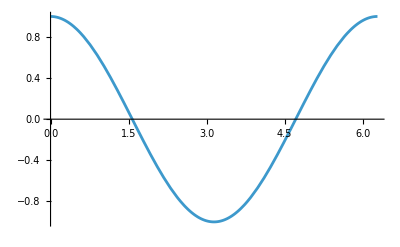
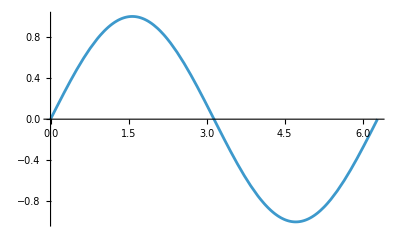

```mathematica
Plot[evecs0th[[1]][[#]]/.kxy2κList,{κ,0,2Pi}]&/@{1,2}
```

The eigenenergy (and therefore the band gap) on a circle around Γ is constant :

```mathematica
Eigensystem[HkagIIPspin0th/.kxy2κList]
```

{{2,1},{{Cot[κ],1},{Cot[κ]-Csc[κ] Sec[κ],1}}}

#### 1 st order perturbation - not needed

Since the off-diagonal terms are of order k^2, we should try to go to 1st order perturbation to get the correct quadratic matrix. However, one sees that the lowest order correction is actually of order k^4, so we can safely ignore this term. In hindsight this is very obvious.

```mathematica
E3Pert=HkagIINicest[[1,1]];
cPert=HkagIINicest[[1,2]];
bPert=HkagIINicest[[1,3]];
HPert1stWithd=Simplify[{{Abs[cPert]^2,cPert*bPert*},{cPert**bPert,Abs[bPert]^2}}/(E0Pert-E3Pert)]/.{kx->d*kx, ky->d*ky};
HPert1st=Simplify[Normal[Series[ComplexExpand[HPert1stWithd],{d,0,4}]]/.d->1,Assumptions->{kx∈Reals,ky∈Reals}];
MatrixForm[HPert1st]
```

((kx^2 ky^2)/12 | 1/24 kx ky (kx^2-ky^2)
1/24 kx ky (kx^2-ky^2) | 1/48 (kx^2-ky^2)^2)

## Shaking Hamiltonian

See my notes on how I got the perturbation term K (which is not Hermitian if Ξ is not purely real), and the definition of Ξ. I am not too confident on whether K is correct. In any case, K is periodic in κ with a period of 2π (or π, since the overall sign gets squared out when finding the transition amplitude).

```mathematica
KShakeKagII={{0,Sin[k.a1]*(Ξ.a1),Sin[k.a2]*(Ξ.a2)},{Sin[k.a1]*(Ξ.a1),0,Sin[k.a3]*(Ξ.a3)},{Sin[k.a2]*(Ξ.a2),Sin[k.a3]*(Ξ.a3),0}};
MatrixForm[KShakeKagII]
```

(0 | Ξ.a1 Sin[k.a1] | Ξ.a2 Sin[k.a2]
Ξ.a1 Sin[k.a1] | 0 | Ξ.a3 Sin[k.a3]
Ξ.a2 Sin[k.a2] | Ξ.a3 Sin[k.a3] | 0)

### Linear shaking

#### Matrix element

This is found by first finding the matrix element between the ground state and the pseudospin basis states, and then forming the superposition of the matrix elements. i.e.,
⟨κ|ψ0⟩ = (A ⟨ψbs1| + B ⟨ψbs2|) |ψ0⟩ = A ⟨ψbs1|ψ0⟩ + B ⟨ψbs2|ψ0⟩ .

```mathematica
KmatPspin1Kag=FullSimplify[ψbs1.KShakeKagII.ψ0];
KmatPspin2Kag=FullSimplify[ψbs2.KShakeKagII.ψ0];
(*1 and 2 above are the two Bloch sphere basis states*)
(*1 and 2 below are the two excited bands*)
(*The ComplexExpand is pretty crucial for some reason*)
KmatKagNearΓ1=Normal[Series[ComplexExpand[evecs0th[[1]].{KmatPspin1Kag,KmatPspin2Kag}/.kNearΓVecList],{d,0,2}]]/.d->1;
KmatKagNearΓ2=Normal[Series[ComplexExpand[evecs0th[[2]].{KmatPspin1Kag,KmatPspin2Kag}/.kNearΓVecList],{d,0,2}]]/.d->1;
(*One can also choose to not expand to O(k), which gives qualitatively identical results*)
(*KmatKagNearΓ1=ComplexExpand[evecs0th[[1]].{KmatPspin1Kag,KmatPspin2Kag}/.kNearΓVecList]/.d->1;
KmatKagNearΓ2=ComplexExpand[evecs0th[[2]].{KmatPspin1Kag,KmatPspin2Kag}/.kNearΓVecList]/.d->1;*)
```

```mathematica
GetMatEleLinShake1=Function[{κ,λ},Simplify[KmatKagNearΓ1/.kxy2κList/.Ξ->{Cos[λ],Sin[λ]}]];
GetExAmpLinShakePspin1=Function[{κ,λ},Simplify[Abs[GetMatEleLinShake1[κ,λ]]^2]];
GetMatEleLinShake2=Function[{κ,λ},Simplify[KmatKagNearΓ2/.kxy2κList/.Ξ->{Cos[λ],Sin[λ]}]];
GetExAmpLinShakePspin2=Function[{κ,λ},Simplify[Abs[GetMatEleLinShake2[κ,λ]]^2]];
```

```mathematica
(*Simplify[KmatKagNearΓ1,Assumptions->{κ,λ}∈Reals]*)
Simplify[GetExAmpLinShakePspin1[κ,λ],Assumptions->{κ,λ}∈Reals]
```

1/8 Sin[2 κ+λ]^2

#### Finding nodes of excitation

The solution can simply be written as 1/2(-λ+πn) for any integer n (or just n = 0,1,2,3) for pseudospin1 (and π/4 away from those for pseudospin2).  The factor of one half is interesting. I assume that this showed up because my perturbation and the state decomposition is k-dependent in a non-trivial way, but I don’t really know for sure.

```mathematica
Reduce[GetExAmpLinShakePspin1[κ,λ]==0,κ,Reals];
Reduce[GetExAmpLinShakePspin2[κ,λ]==0,κ,Reals];
```

```mathematica
lambdaList=Pi*Range[0,1,0.1];
realSolsTable=Association[Table[λval=N[λ0];(*Ensure numerical*)sols=Solve[GetExAmpLinShakePspin1[κ,λval]==0,κ];
realKappa=Select[κ/. sols,Im[#]==0&];
λ0->realKappa,{λ0,lambdaList}]];
numsol=Flatten[KeyValueMap[Function[{λval,κlist},Thread[{λval,κlist}]],realSolsTable],1];
ListPlot[numsol,PlotStyle->PointSize[Medium],AxesLabel->{"λ","κ"},PlotRange->All,AspectRatio->1,GridLines->Automatic,Frame->True,FrameLabel->{"λ","κ"},LabelStyle->{FontSize->14}]
```

C[1]∈ℤ&&(κ==-λ/2+π C[1]||κ==-λ/2+1/2 (π+2 π C[1]))

#### Plots

A few things to notice:

λ’=λ+π should be the same as λ, since they are actually shaking in the same direction.

The excitation pattern simply gets rotated around as one varies λ. In particular, this might mean that a winding number of +2 v.s. -2 can be distinguished based on how the pattern moves around. In the second plot, both traces move in the save direction as λ is varied since they should sum to a constant value.

C3 symmetry is preserved - this is pretty hard to see (took me a whole afternoon to realize, but remember the minus sign in front of λ!)

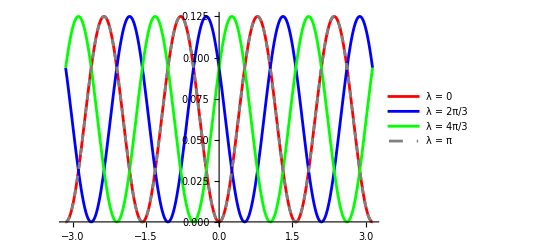

```mathematica
Plot[Evaluate@Table[GetExAmpLinShakePspin1[κ,λ],{λ,{0,2*Pi/3,4*Pi/3,Pi}}],{κ,-Pi, Pi},PlotLegends->Placed[LineLegend[{"λ = 0","λ = 2π/3","λ = 4π/3","λ = π"}],Right],PlotStyle->{Red,Blue,Green,{Gray,Dashed}}]
```

```mathematica
Manipulate[Plot[{GetExAmpLinShakePspin1[κ,λ],GetExAmpLinShakePspin2[κ,λ]},{κ,-Pi,Pi},PlotRange->{0,0.15},AxesLabel->{"κ","Amplitude"},PlotLegends->Placed[LineLegend[{"Band 3 (flat)","Band 2"}],Right]],{{λ,0,"λ"},0,Pi,Appearance->"Labeled"}]
```

### Between the 2nd and 3rd band

The idea is that the off-diagonal component of the Berry connection should be really large between the two bands near Γ, so this is something interesting to look at.

```mathematica
KmatKagNearΓB23=Normal[Series[Simplify[evecs0thFull[[1]].KShakeKagII.evecs0thFull[[2]]/.k->{kx,ky}/.{kx->d kx,ky->d ky}/.ToLatVecList],{d,0,2}]]/.d->1;
GetMatEleLinShakeB23=Function[{κ,λ},Simplify[KmatKagNearΓB23/.kxy2κList/.Ξ->{Cos[λ],Sin[λ]}]];
GetExAmpLinShakePspinB23=Function[{κ,λ},Simplify[Abs[GetMatEleLinShakeB23[κ,λ]]^2]];
Simplify[GetExAmpLinShakePspinB23[κ,λ],Assumptions->{κ,λ}∈Reals]
```

1/4 Sin[κ-λ]^2

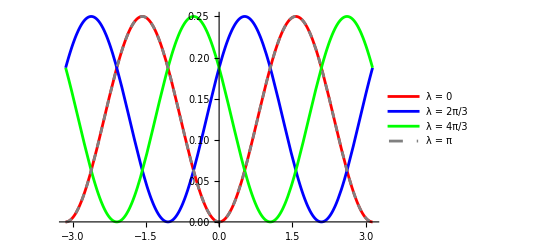

```mathematica
Plot[Evaluate@Table[GetExAmpLinShakePspinB23[κ,λ],{λ,{0,2*Pi/3,4*Pi/3,Pi}}],{κ,-Pi, Pi},PlotLegends->Placed[LineLegend[{"λ = 0","λ = 2π/3","λ = 4π/3","λ = π"}],Right],PlotStyle->{Red,Blue,Green,{Gray,Dashed}}]
```

### Circular shaking

We’ll see that circular shaking doesn’t yield any information on the geometry of the band structure.

#### Matrix elements

```mathematica
GetMatEleCircShake=Function[{κ},Simplify[KmatKagNearΓ1/.{Ξ->{I,1},kx->k*Cos[κ],ky->k*Sin[κ]}]];
GetExAmpCircShake=Function[{κ},Simplify[Abs[GetMatEleCircShake[κ]/.k->1]^2]];
FullSimplify[GetMatEleCircShake[κ],Assumptions->κ∈Reals]
FullSimplify[GetExAmpCircShake[κ],Assumptions->κ∈Reals]
```

((ⅈ+√3) ⅇ^(2 ⅈ κ) √(k^2))/(4 √2)

1/8

#### Plots

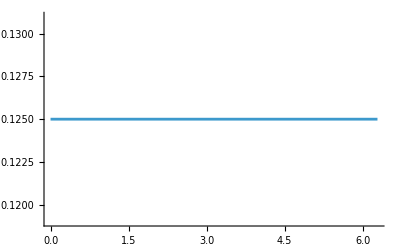

```mathematica
Plot[GetExAmpCircShake[κ],{κ,0,2 Pi}]
```

## Matrix element from Berry connection

The code below moves the k-derivative to the wave functions using the formula in Ozawa et al. (more specifically, the spatially periodic part, i.e. u(k;x), i.e. the information carried in the ψ states I defined). I need at least O(k^2) terms for this. This is again a O(k) correction since ∂ψ/∂k is of order O(k).
Note that this makes it explicit that the matrix element we’re calculating is directly related to the Berry connection. When evaluating the matrix element of the position operator, there is also an intraband component that doesn’t contribute to our calculation, since it doesn’t satisfy Fermi’s golden rule.

### Wrong but kept otherwise I might do it again

Initially I wanted to just write the excited states in the pseudospin basis. Now everything is natually zero because ψ0 is orthogonal to ψbs1 and ψbs2.

```mathematica
(*KagPspinDκ=D[evecs0th/.kxy2κList,κ];
KagPspin1Dkxy=D[evecs0th[[1]],{{kx,ky}}];*)
(*The below is the same as KagPspin1Dkxy.ΞLinShake but with no confusion on order of matrices*)
ΞLinShake={Cos[λ],Sin[λ]};
KagPspinDΞ=ΞLinShake[[1]]*D[evecs0th[[1]],kx]+ΞLinShake[[2]]*D[evecs0th[[1]],ky];
KagPspin2IIDΞ=Simplify[KagPspinDΞ.{ψbs1,ψbs2}];
(*MatrixForm[KagPspin2IIDΞ]*)
Simplify[KagPspin2IIDΞ.ψ0]
```

0

### Unidentified physics-wannabe

Try to calculate the matrix elements with brute force. There is probably a better way to do this, for example by first using /.kxy2κList and then using the chain rule.

```mathematica
KagFull2ndDΞEvec2=ΞLinShake[[1]]*D[evecsHkagIINicestFull2nd[[2]],kx]+ΞLinShake[[2]]*D[evecsHkagIINicestFull2nd[[2]],ky];
KagFull2ndDΞEvec3=ΞLinShake[[1]]*D[evecsHkagIINicestFull2nd[[3]],kx]+ΞLinShake[[2]]*D[evecsHkagIINicestFull2nd[[3]],ky];
(*MatrixForm[KagFull2ndDΞ]*)
(*MatEleLinShakeFull2nd=Simplify[Normal[Series[KagFull2ndDΞ.evecsHkagIINicestFull2nd[[1]]/.kxy2κList,{κ,0,1}]]];*)
MatEleLinShakeFull2ndEvec2=Simplify[KagFull2ndDΞEvec2.evecsHkagIINicestFull2nd[[1]]/.kxy2κList];
MatEleLinShakeFull2ndEvec3=Simplify[KagFull2ndDΞEvec3.evecsHkagIINicestFull2nd[[1]]/.kxy2κList];
```

This still looks similar to what I have from power expansion, except that the nodes are not exactly zero. I think this is really just because of the higher order terms that I threw away.

```mathematica
Manipulate[Plot[{Abs[MatEleLinShakeFull2ndEvec2]^2/.λ->λλ,Abs[MatEleLinShakeFull2ndEvec3]^2/.λ->λλ},{κ,-Pi,Pi},PlotRange->{0,0.025},PlotLegends->{"Evec2","Evec3 (flat)"}],{λλ,0,2*Pi}]
```

## Amplitude modulation

```mathematica
KAmpModGenKagII(*Gen for general*)={{0,M1*Exp[-I*ϕ1]*Cos[k.a1],M2*Exp[-I*ϕ2]*Cos[k.a2]},{M1*Exp[-I*ϕ1]*Cos[k.a1],0,M3*Exp[-I*ϕ3]*Cos[k.a3]},{M2*Exp[-I*ϕ2]*Cos[k.a2],M3*Exp[-I*ϕ3]*Cos[k.a3],0}};
MatrixForm[KAmpModGenKagII]
```

(0 | ⅇ^(-ⅈ ϕ1) M1 Cos[k.a1] | ⅇ^(-ⅈ ϕ2) M2 Cos[k.a2]
ⅇ^(-ⅈ ϕ1) M1 Cos[k.a1] | 0 | ⅇ^(-ⅈ ϕ3) M3 Cos[k.a3]
ⅇ^(-ⅈ ϕ2) M2 Cos[k.a2] | ⅇ^(-ⅈ ϕ3) M3 Cos[k.a3] | 0)

### Matrix elements

```mathematica
KAmpModM12InPhaseKagII=KAmpModGenKagII/.{ϕ1->0,ϕ2->0,ϕ3->0,M1->1,M2->1,M3->0};
KmatAmpModM12InPhasePspin1KagII=FullSimplify[ψbs1.KAmpModM12InPhaseKagII.ψ0];
KmatAmpModM12InPhasePspin2KagII=FullSimplify[ψbs2.KAmpModM12InPhaseKagII.ψ0];
(*1 and 2 above are the two Bloch sphere basis states*)
(*1 and 2 below are the two excited bands*)
(*The ComplexExpand is pretty crucial for some reason*)
KmatAmpModM12InPhaseKagIINearΓ1=Normal[Series[ComplexExpand[evecs0th[[1]].{KmatAmpModM12InPhasePspin1KagII,KmatAmpModM12InPhasePspin2KagII}/.kNearΓVecList],{d,0,2}]]/.d->1;
KmatKagNearΓ2=Normal[Series[ComplexExpand[evecs0th[[2]].{KmatAmpModM12InPhasePspin1KagII,KmatAmpModM12InPhasePspin2KagII}/.kNearΓVecList],{d,0,2}]]/.d->1;
```

```mathematica
GetMatEleAmpModM12InPhaseKag1=Function[{κ},Simplify[KmatAmpModM12InPhaseKagIINearΓ1/.kxy2κList]];
GetExAmpAmpModM12InPhaseKag1=Function[{κ},Simplify[Abs[GetMatEleAmpModM12InPhaseKag1[κ]]^2]];
GetMatEleAmpModM12InPhaseKag2=Function[{κ},Simplify[KmatAmpModM12InPhaseKagIINearΓ2/.kxy2κList]];
GetExAmpAmpModM12InPhaseKag2=Function[{κ},Simplify[Abs[GetMatEleAmpModM12InPhaseKag2[κ]]^2]];
```

```mathematica
Simplify[ComplexExpand[GetExAmpAmpModM12InPhaseKag1[κ]],Assumptions->κ∈Reals]
Simplify[ComplexExpand[GetExAmpAmpModM12InPhaseKag2[κ]],Assumptions->κ∈Reals]
Reduce[Simplify[ComplexExpand[GetExAmpAmpModM12InPhaseKag1[κ]],Assumptions->κ∈Reals]==0,κ,Reals]
Reduce[Simplify[ComplexExpand[GetExAmpAmpModM12InPhaseKag2[κ]],Assumptions->κ∈Reals]==0,κ,Reals]
(*Reduce[GetExAmpAmpModM12InPhaseKag1[κ]==0,κ,Reals]
Reduce[GetExAmpAmpModM12InPhaseKag2[κ]==0,κ,Reals]*)
```

(58+45 Cos[2 κ]-20 Cos[4 κ]-8 Cos[6 κ]+45 √3 Sin[2 κ]+20 √3 Sin[4 κ])/1152

(50+60 Cos[2 κ]+11 Cos[4 κ]-12 √3 Sin[2 κ]-5 √3 Sin[4 κ])/1152

C[1]∈ℤ&&(κ==1/2 (-(2 π)/3+2 π C[1])||κ==1/2 (2 ArcTan[]+2 π C[1])||κ==1/2 (2 ArcTan[]+2 π C[1]))

False

### Plots

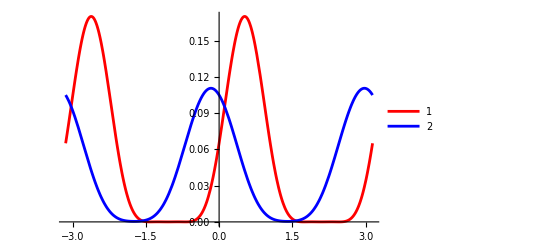

```mathematica
Plot[{GetExAmpAmpModM12InPhaseKag1[κ],GetExAmpAmpModM12InPhaseKag2[κ]},{κ,-Pi, Pi},PlotLegends->Placed[LineLegend[{"1","2"}],Right],PlotStyle->{Red,Blue}]
```

## Kagome lattice - Expansion around K and K’

## Constants

I will use the eigenstates of the mirror symmetry operator My as the basis for the two lower bands.

```mathematica
ψy1Γ
ψy2Γ
testmat=HkagII/.kNearKbVecList/.kxy2ZeroList
HkagIIatK
Simplify[Eigensystem[HkagIIatK]]
```

{-1/(√2),1/(√2),0}

{1/(√6),1/(√6),-√(2/3)}

{{0,1,-1},{1,0,-1},{-1,-1,0}}

{{0,1,-1},{1,0,-1},{-1,-1,0}}

{{2,-1,-1},{{-1,-1,1},{1,0,1},{-1,1,0}}}

### New basis states

## Lieb-kagome lattice - expand near emerging Dirac points

## Constants

I will use the eigenstates of the mirror symmetry operator My as the basis for the excited bands. Note that they have opposite eigenvalues for My.

```mathematica
rLk=0.8;
Assert[1>=rLk>=0]
```

### New basis states

Since away from the high symmetry line we don’t expect ψy1Γ and ψy2Γ to be eigenstates of the hamiltonian, but they should be on the high symmetry line, the weight between ψy1Γ and ψy2Γ should vary as a function of angle. I’ll similarly guess that the nice basis for our Bloch sphere picture will be given by the superposition of these two states with equal weight and perhaps some non-trivial relative phase.

```mathematica
ψyt1=Simplify[(ψy1Γ+Exp[I*τ]*ψy2Γ)/Sqrt[2]];
ψyt2=Simplify[(ψy1Γ-Exp[I*τ]*ψy2Γ)/Sqrt[2]];
ψybs1=ψyt1/.τ->0;
ψybs2=ψyt2/.τ->0;
```

### Unitary matrices for basis transformation

```mathematica
Uytau={ψ0,ψyt1,ψyt2};
Uybs={ψ0,ψybs1,ψybs2};
```

## Lieb-kagome lattice Hamiltonian

```mathematica
HLkII=-2*{{0,r*Cos[k.a1],Cos[k.a2]},{r*Cos[k.a1],0,Cos[k.a3]},{Cos[k.a2],Cos[k.a3],0}};
```

### Sanity checks

It is easy to see that My should commute with the Hamiltonian for kx = 0. But since H(k) = H(-k), the commutation relation also holds for ky = 0:

```mathematica
HLkIIalongky=HLkII/.kNearΓVecList/.{kx->0,d->1};
HLkIIalongkx=HLkII/.kNearΓVecList/.{ky->0,d->1};
HLkIIalongky.MyII-MyII.HLkIIalongky
HLkIIalongkx.MyII-MyII.HLkIIalongkx
```

{{0,0,0},{0,0,0},{0,0,0}}

{{0,0,0},{0,0,0},{0,0,0}}

### Position of the Dirac points

Note that the Dirac point split from the QBTP is spawn along the kx-axis. The bands were not ordered in energy. Also, while there appears to be a completely flat band, it is only flat along this high symmetry line.

```mathematica
(*r->rLK must be applied after the Simplify below*)
{evalsHLkalongkx,evecsHLkalongkx}=Simplify[Eigensystem[HLkIIalongkx/.d->1],Assumptions->1>=r>=0];
```

Let’s visualize this at the value of r chosen:

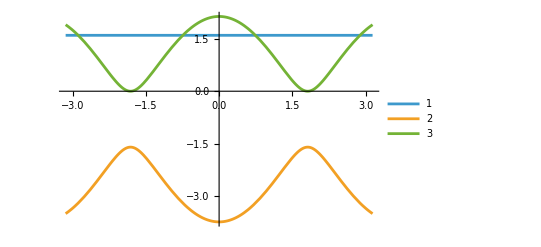

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{kx→-ArcCos[-1+2 r^2]/(√3)},{kx→ArcCos[-1+2 r^2]/(√3)}}

```mathematica
Plot[Evaluate[evalsHLkalongkx/.r->rLk],{kx,-Pi,Pi},PlotLegends->{"1","2","3"}]
{LkDiracPtkx1,LkDiracPtkx2}=Solve[evalsHLkalongkx[[1]]-evalsHLkalongkx[[3]]==0,kx]
kNearLkDP1={d*kx-Values[LkDiracPtkx1][[1]],d*ky};
kNearLkDP2={d*kx-Values[LkDiracPtkx2][[1]],d*ky};(*d is a dummy variable for series expansion*)
Lk1VecList=Append[ToLatVecList,k->kNearLkDP1];
Lk2VecList=Append[ToLatVecList,k->kNearLkDP2];
```

#### Expansion around the Dirac points

We only expand to lowest order in k.

```mathematica
HLkIItau=Uytau.HLkII.Inverse[Uytau];
HLkIIDP1tauPwr1=FullSimplify[Normal[Series[HLkIItau/.Lk1VecList,{d,0,1}]]/.d->1,Assumptions->1>=r>=0];
HLkIIDP2tauPwr1=FullSimplify[Normal[Series[HLkIItau/.Lk2VecList,{d,0,1}]]/.d->1,Assumptions->1>=r>=0];(*Much better than Simplify in this case*)
```

### Playing around with τ

τ=0 seems good. Other choices will leave both kx and ky in the off-diagonal terms in the effective two-band hamiltonian.

```mathematica
MatrixForm[Simplify[HLkIIDP1tauPwr1/.τ->0]](*Insert your favorite τ here*)
(*MatrixForm[Simplify[HLkIIDP2tauPwr1/.τ->0]](*Insert your favorite τ here*)*)
HLkIIDP1Nicest=Simplify[HLkIIDP1tauPwr1/.τ->0];
HLkIIDP2Nicest=Simplify[HLkIIDP2tauPwr1/.τ->0];
```

(-4/3 (3 r-kx √(3-3 r^2)) | 1/3 (-kx+ky) √(3-3 r^2) | 1/3 (kx+ky) √(3-3 r^2)
1/3 (-kx+ky) √(3-3 r^2) | 2 r-2/3 (kx+ky) √(3-3 r^2) | 2/3 kx √(3-3 r^2)
1/3 (kx+ky) √(3-3 r^2) | 2/3 kx √(3-3 r^2) | 2 r+2/3 (-kx+ky) √(3-3 r^2))

This is really weird - I thought I’ll get My symmetry, i.e. the first should be zero but not the second

```mathematica
Simplify[HLkIIDP1Nicest - (HLkIIDP2Nicest /.{kx->-kx,ky->ky})]
Simplify[HLkIIDP1Nicest - (HLkIIDP2Nicest /.{kx->-kx,ky->-ky})]
```

{{0,(2 ky √(1-r^2))/(√3),(2 ky √(1-r^2))/(√3)},{(2 ky √(1-r^2))/(√3),-(4 ky √(1-r^2))/(√3),0},{(2 ky √(1-r^2))/(√3),0,(4 ky √(1-r^2))/(√3)}}

{{0,0,0},{0,0,0},{0,0,0}}

### The case of τ = 0

#### 0th order perturbation

```mathematica
HLkDP1Pspin0th=HLkIIDP1Nicest[[2;;3,2;;3]];
HLkDP2Pspin0th=HLkIIDP2Nicest[[2;;3,2;;3]];
(*MatrixForm[HLkIIDP1Nicest]*)
MatrixForm[HLkDP1Pspin0th]
```

(2 r-2/3 (kx+ky) √(3-3 r^2) | 2/3 kx √(3-3 r^2)
2/3 kx √(3-3 r^2) | 2 r+2/3 (-kx+ky) √(3-3 r^2))

Interestingly, one finds that the eigenstates around the Dirac points are independent of r, although the eigenvalues does:

```mathematica
{evalsHLkDP1Pspin0th,evecsHLkDP1Pspin0thRaw}=Simplify[Eigensystem[HLkDP1Pspin0th],Assumptions->{{kx,ky}∈Reals,1>=r>=0}]
evecsHLkDP1Pspin0th=Simplify[Normalize[#]&/@evecsHLkDP1Pspin0thRaw,Assumptions->{kx,ky}∈Reals];
{evalsHLkDP2Pspin0th,evecsHLkDP2Pspin0thRaw}=Simplify[Eigensystem[HLkDP2Pspin0th],Assumptions->{{kx,ky}∈Reals,1>=r>=0}];
evecsHLkDP2Pspin0th=Simplify[Normalize[#]&/@evecsHLkDP2Pspin0thRaw,Assumptions->{kx,ky}∈Reals];
```

{{-2/3 (-3 r+kx √(3-3 r^2)+√3 √((kx^2+ky^2) (1-r^2))),2 r+(2 (-kx √(1-r^2)+√(-((kx^2+ky^2) (-1+r^2)))))/(√3)},{{-(ky+√(kx^2+ky^2))/kx,1},{(-ky+√(kx^2+ky^2))/kx,1}}}

#### 1st order perturbation - not needed for linear touching

This is again obvious from the fact that the off-diagonal terms that couples to the ground band is linear order (and have no constant terms, i.e. is homogeneous).

## Shaking Hamiltonian

```mathematica
KshakeLk={{0,r*Sin[k.a1]*(Ξ.a1),Sin[k.a2]*(Ξ.a2)},{r*Sin[k.a1]*(Ξ.a1),0,Sin[k.a3]*(Ξ.a3)},{Sin[k.a2]*(Ξ.a2),Sin[k.a3]*(Ξ.a3),0}};
MatrixForm[KshakeLk]
```

(0 | r Ξ.a1 Sin[k.a1] | Ξ.a2 Sin[k.a2]
r Ξ.a1 Sin[k.a1] | 0 | Ξ.a3 Sin[k.a3]
Ξ.a2 Sin[k.a2] | Ξ.a3 Sin[k.a3] | 0)

### Linear shaking

#### Matrix elements

Even though we are no longer centered around a high symmetry point, I still assume that the ground band state doesn’t change too much.

```mathematica
(*Simplify in the next cell doesn't make this simplification, but using FullSimplify makes the execution too long*)
(*FullSimplify[Cos[1/2 ArcCos[-1+2 r^2]],Assumptions->1>=r>=0]
FullSimplify[Sin[1/2 ArcCos[-1+2 r^2]],Assumptions->1>=r>=0]*)
simplifyHelperList={Cos[1/2 ArcCos[-1+2 r^2]]->r,Sin[1/2 ArcCos[-1+2 r^2]]->√(1-r^2)};
```

```mathematica
KmatPspin1Lk=FullSimplify[ψybs1.KshakeLk.ψ0];
KmatPspin2Lk=FullSimplify[ψybs2.KshakeLk.ψ0];
(*1 and 2 above are the two Bloch sphere basis states*)
(*1 and 2 below are the two Dirac points of the same band*)
KmatLkNearDP1=Simplify[Normal[Series[evecsHLkDP1Pspin0th[[1]].{KmatPspin1Lk,KmatPspin2Lk}/.Lk1VecList,{d,0,2}]]/.d->1/.simplifyHelperList,Assumptions->{{kx,ky}∈Reals,1>=r>=0}];
KmatLkNearDP2=Simplify[Normal[Series[evecsHLkDP2Pspin0th[[1]].{KmatPspin1Lk,KmatPspin2Lk}/.Lk2VecList,{d,0,2}]]/.d->1/.simplifyHelperList,Assumptions->{{kx,ky}∈Reals,1>=r>=0}];
```

```mathematica
fSimpHelperList={Pi>=κ>=-Pi,Pi>=λ>=-Pi,1>=r>=0};
GetLkDP1MatEleLinShake=Function[{κ,λ},FullSimplify[KmatLkNearDP1/.kxy2κList/.Ξ->{Cos[λ],Sin[λ]},Assumptions->fSimpHelperList]];
GetLkDP1ExAmpLinShake=Function[{κ,λ,rr},FullSimplify[Abs[GetLkDP1MatEleLinShake[κ,λ]/.r->rr]^2,Assumptions->fSimpHelperList]];
GetLkDP2MatEleLinShake=Function[{κ,λ},FullSimplify[KmatLkNearDP2/.kxy2κList/.Ξ->{Cos[λ],Sin[λ]},Assumptions->fSimpHelperList]];
GetLkDP2ExAmpLinShake=Function[{κ,λ,rr},FullSimplify[Abs[GetLkDP2MatEleLinShake[κ,λ]/.r->rr]^2,Assumptions->fSimpHelperList]];
```

#### Position of nodes

The position of nodes is pretty nontrivial. Even the numerical solver seems to need some help to remove some prefactors that won’t affect the position of nodes. Very interestingly there are three nodes.

```mathematica
(*This term appears during simplification and is never zero*)
Reduce[Sec[1/4 (π+2 κ)] √(1-Sin[κ])==0,κ,Reals]
```

False

```mathematica
Step1LkDP1MatEle=FullSimplify[TrigFactor[GetLkDP1MatEleLinShake[κ,λ,r]],Assumptions->fSimpHelperList];
Step2LkDP1MatEle=Step1LkDP1MatEle/(1/(16 √3)Sec[1/4 (π+2 κ)] √(1-Sin[κ]))
```

4 √3 r Cos[(3 κ)/2+λ]+√(1-r^2) (-Cos[(5 κ)/2-λ]+6 Cos[κ/2+λ]+2 Sin[κ/2] Sin[2 κ+λ])

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

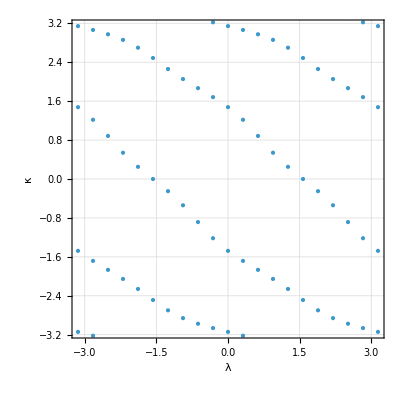

```mathematica
(*Reduce[Step2LkDP1MatEle==0&&1>=r>=0&&λ∈Reals,κ,Reals]*)
lambdaList=Pi*Range[-1,1,0.1];
LHSrealSol=Function[{κin,λin},Step2LkDP1MatEle/.{r->rLk,κ->κin,λ->λin}];
realSolsTable=Association[Table[λval=N[λ0];(*Ensure numerical*)sols=Solve[LHSrealSol[κ,λval]==0,κ];
realKappa=Select[κ/. sols,Im[#]==0&];
λ0->realKappa,{λ0,lambdaList}]];
numsol=Flatten[KeyValueMap[Function[{λval,κlist},Thread[{λval,κlist}]],realSolsTable],1];
ListPlot[numsol,PlotStyle->PointSize[Medium],Axes->False,(*disable duplicate axes*)PlotRange->{-Pi,Pi},AspectRatio->1,GridLines->Automatic,Frame->True,FrameLabel->{"λ","κ"},LabelStyle->{FontSize->14}]
(*Manipulate[Plot[Step2LkDP1MatEle/.r->rLk/.λ->λλ,{κ,-Pi,Pi},PlotRange->{-10,10}],{{λλ,0,"λ"},0,Pi,Appearance->"Labeled"}]*)
```

#### Plots

xy-plot is not so useful in visualizing the excitation pattern, but is good for getting a feeling of the actual values of the matrix elements.

```mathematica
Manipulate[Plot[{GetLkDP1ExAmpLinShake[κ,λ,rLk],GetLkDP2ExAmpLinShake[κ,λ,rLk]},{κ,-Pi,Pi},PlotRange->{0,0.3},AxesLabel->{"κ","Amplitude"},PlotLegends->Placed[LineLegend[{"DP1","DP2"}],Right]],{{λ,0,"λ"},0,Pi,Appearance->"Labeled"}]
```

Both patterns move counterclockwise as λ is increased, which is a result of the weird symmetry above. Is this telling us that the winding number around each of the Dirac point is indeed of the same sign? If so, the “weird” symmetry is actually expected

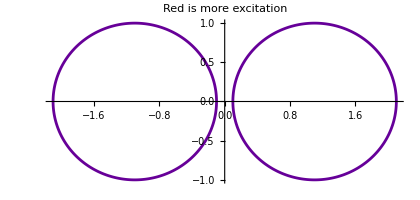

```mathematica
colorFunc[val_]:=Blend[{Blue,Red},Rescale[Sqrt[val],{0,0.5}]]
λPrmPlot=0;
CircLkDP1ExAmpLinShake=ParametricPlot[{-1.1,0}+{Cos[κ],Sin[κ]},{κ,-Pi,Pi},ColorFunction->Function[{x,y,κ},colorFunc[GetLkDP1ExAmpLinShake[κ,λPrmPlot,rLk]]],ColorFunctionScaling->False];
CircLkDP2ExAmpLinShake=ParametricPlot[{1.1,0}+{Cos[κ],Sin[κ]} ,{κ,-Pi,Pi},ColorFunction->Function[{x,y,κ},colorFunc[GetLkDP2ExAmpLinShake[κ,λPrmPlot,rLk]]],ColorFunctionScaling->False];
Show[CircLkDP1ExAmpLinShake,CircLkDP2ExAmpLinShake,PlotRange->All,PlotLabel->"Red is more excitation"]
```

### Circular shaking

This doesn’t seem to tell us much.

```mathematica
GetLkDP1MatEleCircShake=Function[{κ,rin},FullSimplify[KmatLkNearDP1/.kxy2κList/.Ξ->{I,1}/.r->rin,Assumptions->fSimpHelperList]];
GetLkDP1ExAmpCircShake=Function[{κ,rin},FullSimplify[Abs[GetLkDP1MatEleCircShake[κ,rin]]^2,Assumptions->fSimpHelperList]];
GetLkDP2MatEleCircShake=Function[{κ,rin},FullSimplify[KmatLkNearDP2/.kxy2κList/.Ξ->{I,1}/.r->rin,Assumptions->fSimpHelperList]];
GetLkDP2ExAmpCircShake=Function[{κ,rin},FullSimplify[Abs[GetLkDP2MatEleCircShake[κ,rin]]^2,Assumptions->fSimpHelperList]];
```

#### Plots

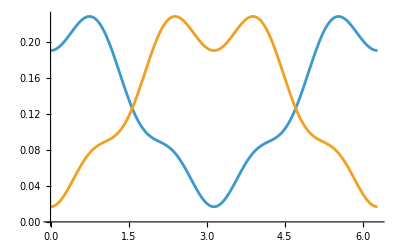

```mathematica
Plot[{GetLkDP1ExAmpCircShake[κ,rLk],GetLkDP2ExAmpCircShake[κ,rLk]},{κ,0,2 Pi}]
```

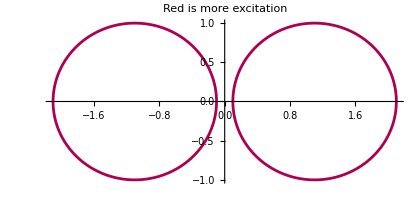

```mathematica
CircLkDP1ExAmpCircShake=ParametricPlot[{-1.1,0}+{Cos[κ],Sin[κ]},{κ,-Pi,Pi},ColorFunction->Function[{x,y,κ},colorFunc[GetLkDP1ExAmpCircShake[κ,rLk]]],ColorFunctionScaling->False];
CircLkDP2ExAmpCircShake=ParametricPlot[{1.1,0}+{Cos[κ],Sin[κ]} ,{κ,-Pi,Pi},ColorFunction->Function[{x,y,κ},colorFunc[GetLkDP2ExAmpCircShake[κ,rLk]]],ColorFunctionScaling->False];
Show[CircLkDP1ExAmpCircShake,CircLkDP2ExAmpCircShake,PlotRange->All,PlotLabel->"Red is more excitation"]
```